# Recent fees

```mathematica
Clear["Global`"];
server="localhost";
db=DatabaseReference[
<| "Backend" ->"PostgreSQL"
, "Name"->"bitcoin"
, "Port"-> Automatic
, "Host"->server
,"Username"->"rpc"
,"Password"->"YOURPASSWORD"|>
];
```

## Recent subsidy and fees by day

```mathematica
dailyfees = ExternalEvaluate[
db
,"select to_timestamp(time)::date as date
, count(*) as blocks
, sum(txs)::int as txs
, sum(subsidy) as subsidy
, sum(totalfee) as totalfee 
from blockstats 
group by 1
order by 1 desc;"
]
```

Dataset[<>]

## Fees by epoch (2016 blocks)

```mathematica
epochdata = ExternalEvaluate[
db
,"select Ceiling(height/2016 + 1)::int as epoch 
, to_timestamp(min(time))::date as start
, to_timestamp(max(time))::date as end
, count(*)::int as blocks 
, sum(txs)::int as txs 
, sum(subsidy) as subsidy 
, sum(totalfee) as totalfee  
from blockstats 
group by 1 order by 1 desc;"
]
```

## Fees by epoch (2016 blocks)

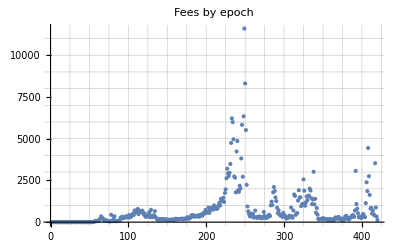

```mathematica
epochfeedata ={#"epoch",#"totalfee"}&/@epochdata;
ListPlot[epochfeedata
,PlotRange->All
, ImageSize->Full
, GridLines->All
, PlotLabel->"Fees by epoch"
, ImageSize->Full
]
```

## Transactions by epoch (2016 blocks)

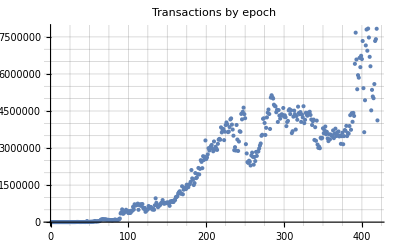

```mathematica
epochtxdata ={#"epoch",#"txs"}&/@epochdata;
ListPlot[epochtxdata
,PlotRange->All
, ImageSize->Full
, GridLines->All
, PlotLabel->"Transactions by epoch"
, ImageSize->Full
]
```

## All time subsidy + fees

```mathematica
txs = ExternalEvaluate[
db
,"select height
, subsidy
, totalfee
from blockstats
order by height desc"];
data={#"height",#"subsidy"+#"totalfee"}&/@txs;
```

```mathematica
ListPlot[data
,PlotRange->All
, ImageSize->Full
, GridLines->{
Range[0,10^6,210000]
,Join[Range[0,500,50],{25,12.5,6.25,.3125}]
}
,PlotLegends->{"Height", "BTC"}
, PlotLabel->"All time subsidy + fees"
]
```

-Graphics-

## Subsidy + fees, last 10,000 blocks

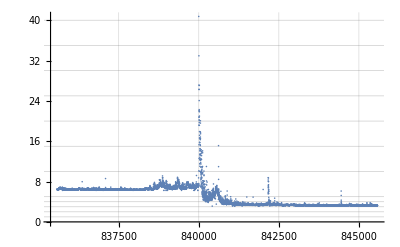

```mathematica
data10k=Take[data,10000];
ListPlot[data10k
,PlotRange->All
,ImageSize->Full
, GridLines->{Automatic,Join[Range[4],Range[0,50,5]]}
]
```

## Largest fee blocks, all time

```mathematica
Take[ReverseSortBy[data,Last ],50]
```